```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\jedli\OneDrive - NUS High School\Documents\Computing Studies\computed_tomography\logs

```mathematica
data=Import["masked_sinograms/data.csv"];
data=Table[data[[i]],{i,2,Length[data]}];
```

```mathematica
data[[1]]
```

{0,0,0.0174052,0.0174052,0.079072,0.079072,35.5293,35.5293,0.84353,0.84353}

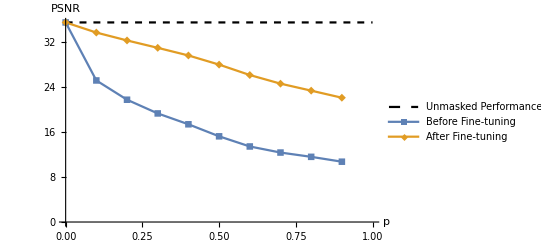

```mathematica
ListPlot[{{{0,data[[1]][[7]]},{1,data[[1]][[7]]}},Map[{#[[2]],#[[7]]}&,data],Map[{#[[2]],#[[8]]}&,data]},AxesLabel->{"p","PSNR"},AxesStyle->Directive[Black,Thickness[0.003]],PlotStyle->{Directive[Black,Dashed],ColorData[97,1],ColorData[97,2]},PlotLegends->Placed[{"Unmasked Performance","Before Fine-tuning", "After Fine-tuning"},{0.31,0.19}],Joined->True,PlotMarkers->{None,Automatic,Automatic}]
```